```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQp[n_]:=If[PrimeQ[n]&&n>0,True,False]
```

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes

Arithmetic Functions

## Moebius Function

### Definition

The Moebius function is defined as follows:
μ(1) = 1;
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
μ(n) = (-1)^k if α_i=1
μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,12}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0

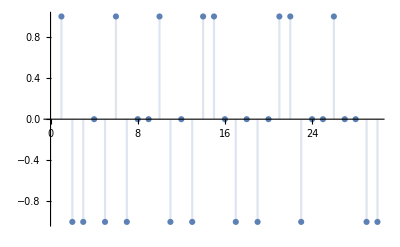

```mathematica
DiscretePlot[MoebiusMu[k],{k,30},AxesOrigin->{0,0}]
```

## Euler totient Function

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

[ ToDo ] Sum formula:

[ ToDo ] Product formula:

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,18}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6

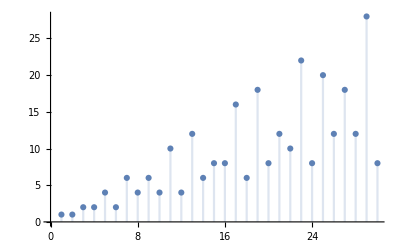

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example-TMP